```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY196/sec_int_data/610nm.dat"]
```

{{1.64105,0.237046},{1.57964,0.236415},{1.51907,0.262133},{1.47433,0.26582},{1.70936,0.236889},{1.78557,0.231191}}

0.423404-0.110302 x

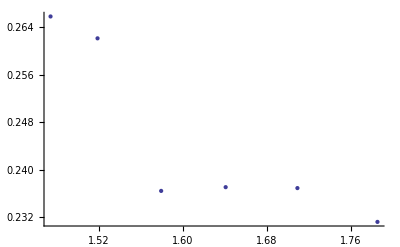

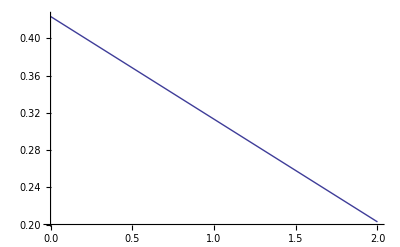

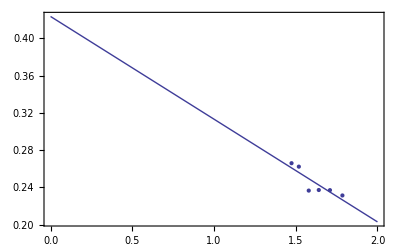

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```